```mathematica
Subscript[H, JRM]=-4EJ(Cos[Subscript[φ, ext]/4]Cos[Subscript[φ, x]/2]Cos[Subscript[φ, y]/2]Cos[Subscript[φ, z]]+Sin[Subscript[φ, ext]/4]Sin[Subscript[φ, x]/2]Sin[Subscript[φ, y]/2]Sin[Subscript[φ, z]]);
Subscript[H, cros]=-EJ(Cos[Subscript[φ, L1]]+Cos[Subscript[φ, L2]]+Cos[Subscript[φ, L3]]+Cos[Subscript[φ, L4]]);
({{Subscript[φ, a]}, {Subscript[φ, b]}, {Subscript[φ, c]}, {Subscript[φ, d]}})=({{1/2, 1/2, 1, 1/4}, {-1/2, 1/2, -1, 1/4}, {-1/2, -1/2, 1, 1/4}, {1/2, -1/2, -1, 1/4}}).({{Subscript[φ, x]}, {Subscript[φ, y]}, {Subscript[φ, z]}, {Subscript[φ, M]}});

solvecros=Flatten[Simplify[Solve[Subscript[φ, a]-Subscript[φ, L1]+Subscript[φ, L2]==Subscript[φ, ext]/4+2Pi Subscript[n, a]&&Subscript[φ, b]-Subscript[φ, L2]+Subscript[φ, L3]==Subscript[φ, ext]/4+2Pi Subscript[n, b]&&Subscript[φ, c]-Subscript[φ, L3]+Subscript[φ, L4]==Subscript[φ, ext]/4+2Pi Subscript[n, c]&&Subscript[φ, L1]+Subscript[φ, L2]+Subscript[φ, L3]+Subscript[φ, L4]==0,{Subscript[φ, L1],Subscript[φ, L2],Subscript[φ, L3],Subscript[φ, L4]}]/.Subscript[φ, M]->Subscript[φ, ext]+2Pi(Subscript[n, a]+Subscript[n, b]+Subscript[n, c]+Subscript[n, d])]/.{Subscript[n, a]->m,Subscript[n, b]->m,Subscript[n, c]->m,Subscript[n, d]->m}]
```

{φ_L1→1/4 (2 φ_y+2 φ_z),φ_L2→1/4 (-2 φ_x-2 φ_z),φ_L3→1/4 (-2 φ_y+2 φ_z),φ_L4→1/4 (2 φ_x-2 φ_z)}

```mathematica
Subscript[H, cros]=Subscript[H, cros]/.solvecros
```

-EJ (Cos[1/4 (-2 φ_x-2 φ_z)]+Cos[1/4 (2 φ_x-2 φ_z)]+Cos[1/4 (-2 φ_y+2 φ_z)]+Cos[1/4 (2 φ_y+2 φ_z)])

```mathematica
H=Subscript[H, JRM]+Subscript[H, cros]
```

-EJ (Cos[1/4 (-2 φ_x-2 φ_z)]+Cos[1/4 (2 φ_x-2 φ_z)]+Cos[1/4 (-2 φ_y+2 φ_z)]+Cos[1/4 (2 φ_y+2 φ_z)])-4 EJ (Cos[φ_ext/4] Cos[φ_x/2] Cos[φ_y/2] Cos[φ_z]+Sin[φ_ext/4] Sin[φ_x/2] Sin[φ_y/2] Sin[φ_z])

```mathematica
Hx=Series[H,{Subscript[φ, x],0,4}]//Function[Y,Normal[Y+O[Subscript[φ, x]]^5]];
Hxy=Series[Hx,{Subscript[φ, y],0,4}]//Function[Y,Normal[Y+O[Subscript[φ, y]]^5]];
Hxyz=Series[Hxy,{Subscript[φ, z],0,4}]//Function[Y,Normal[Y+O[Subscript[φ, z]]^5]];
```

```mathematica
cool=CoefficientRules[Hxyz,{Subscript[φ, x],Subscript[φ, y],Subscript[φ, z]}];
power=Table[cool[[i,1,1]]+cool[[i,1,2]]+cool[[i,1,3]],{i,1,Length[cool]}];
hi=Flatten[Table[Flatten[Position[power,i]],{i,0,4}]];
hihi=Table[cool[[hi[[i]]]],{i,1,Length[hi]}];
For[i=1,i≤Length[hihi],i++,
hihi[[i,2]]=Collect[Simplify[hihi[[i,2]]],EJ]
]
hihi
```

{{0,0,0}→-8 EJ Cos[φ_ext/8]^2,{2,0,0}→1/4 EJ (1+2 Cos[φ_ext/4]),{0,2,0}→1/4 EJ (1+2 Cos[φ_ext/4]),{0,0,2}→1/2 EJ (1+4 Cos[φ_ext/4]),{1,1,1}→-EJ Sin[φ_ext/4],{4,0,0}→-1/192 EJ (1+2 Cos[φ_ext/4]),{2,2,0}→-1/16 EJ Cos[φ_ext/4],{2,0,2}→-1/32 EJ (1+8 Cos[φ_ext/4]),{0,4,0}→-1/192 EJ (1+2 Cos[φ_ext/4]),{0,2,2}→-1/32 EJ (1+8 Cos[φ_ext/4]),{0,0,4}→-1/96 EJ (1+16 Cos[φ_ext/4])}

```mathematica
Plus@@(hihi/.Rule[{a_,b_,c_},d_]:>Subscript[φ, XJ]^a Subscript[φ, YJ]^b Subscript[φ, ZJ]^c d);
H=Collect[Plus@@(hihi/.Rule[{a_,b_,c_},d_]:>Subscript[φ, XJ]^a Subscript[φ, YJ]^b Subscript[φ, ZJ]^c d),{EJ(1+2  Cos[Subscript[φ, ext]/4]),EJ (1+4 Cos[Subscript[φ, ext]/4]),-1/32 EJ (1+8 Cos[Subscript[φ, ext]/4]),EJ (1+16 Cos[Subscript[φ, ext]/4])}]
```

-8 EJ Cos[φ_ext/8]^2-1/16 EJ Cos[φ_ext/4] φ_XJ^2 φ_YJ^2+EJ (1+2 Cos[φ_ext/4]) (φ_XJ^2/4-φ_XJ^4/192+φ_YJ^2/4-φ_YJ^4/192)-EJ Sin[φ_ext/4] φ_XJ φ_YJ φ_ZJ+1/2 EJ (1+4 Cos[φ_ext/4]) φ_ZJ^2-1/96 EJ (1+16 Cos[φ_ext/4]) φ_ZJ^4-1/32 EJ (1+8 Cos[φ_ext/4]) (φ_XJ^2 φ_ZJ^2+φ_YJ^2 φ_ZJ^2)

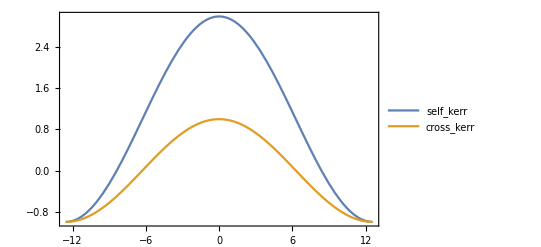

```mathematica
Plot[{(1+2 Cos[Subscript[φ, ext]/4]),Cos[Subscript[φ, ext]/4]},{Subscript[φ, ext],-4π,4π},PlotRange->All,Frame->True,PlotLegends->{"self_kerr","cross_kerr"}]
```